# Контролна работа №1 Група А, задача 1 Фак. №2001261051

## Дадено е уравнението: -2 x^3 - (b + 40).cosx - 5.(a + b + 1) = 0

```mathematica
f[x_] := -2 x^3 -41Cos[x] - 35
```

### 1. Да се намери броят на корените на уравнението

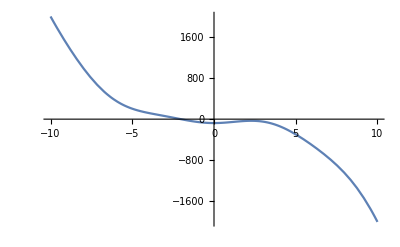

```mathematica
Plot[f[x], {x, -10, 10}]
```

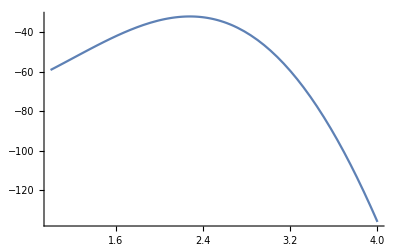

```mathematica
Plot[f[x], {x, 1, 4}]
```

Няма корен в този интервал!

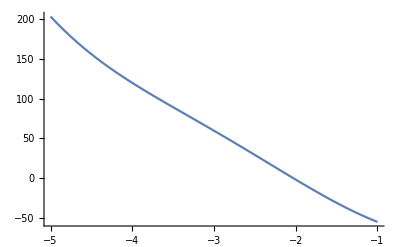

```mathematica
Plot[f[x], {x, -5, -1}]
```

Брой корени: 1

### 2. Да се локализира най-малкият от тях (в случай на повече от един) в интервала [p, q]

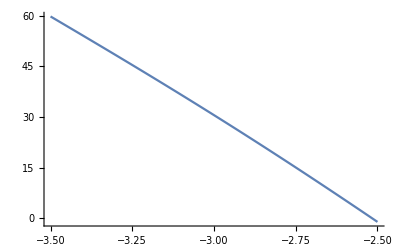

```mathematica
Plot[f[x], {x, -3.5, -2.5}]
```

```mathematica
f[-3.5]
```

59.7635

```mathematica
f[-2.5]
```

-1.09625

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус).
(2) f(-3.5) = 59.7635 ... > 0 и f(-2.5) = -1.09625 ... < 0
=> Функцията има различни знаци в двата края на разглеждания интервал [-4; -1].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [-4; -1].

### 3. Да се опедели началното приближение и постоянната точка за метода на хордите

Избор на начално приближение и постоянна точка
Нужно е да е изпълнено условието f(x0).f’’(x) < 0
В нашия случай f’’(x) < 0. Следователно е нужно f(x0) > 0

```mathematica
f[-3.5]
```

59.7635

```mathematica
f[-2.5]
```

-1.09625

```mathematica
p = -2.5
```

-2.5

```mathematica
x0 = -3.5
```

-3.5

### 4. Да се проверят условията за метода на хордите

#### Проверка на сходимост:

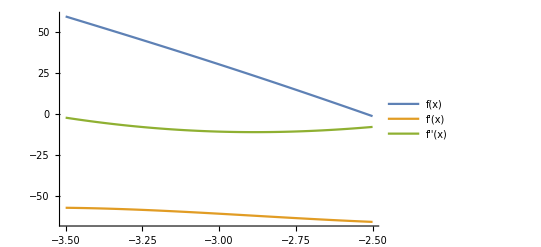

```mathematica
Plot[{f[x],f'[x], f''[x]}, {x,-3.5, -2.5}, PlotLegends->"Expressions"]
```

#### Графика на първата производна

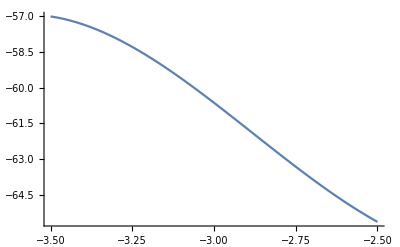

```mathematica
Plot[f'[x],{x,-3.5,-2.5}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [-3.5; -2.5] са между -65 и -55. Следователно първата f'(x) < 0 в целия разглеждан интервал [-3.5; -2.5].

#### Графика на втората производна

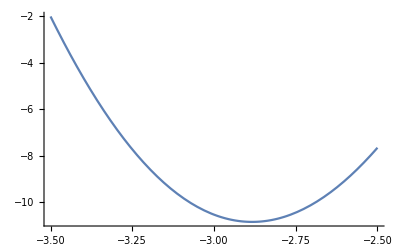

```mathematica
Plot[f''[x],{x,-3.5,-2.5}]
```

Извод : (2) Стойностите на втората производна в разглеждания интервал [-3.5; -2.5] са между -10 и - 1. Следователно втората f'' (x) < 0 в целия разглеждан интервал [-3.5; -2.5].

Извод: От (1) и (2) следва, че първата и втората производна имат постоянни знаци в разглеждания интервал [-3.5; -2.5]. Следователно условията за сходимост на метода на хордите са изпълнени.

### 5. Да се направят 3 итерации по метода на хордите

```mathematica
For[n = 0, n <= 3, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1];
x0 = x1
]
```

n = 0 x_n = -2.51801

n = 1 x_n = -2.51672

n = 2 x_n = -2.51672

n = 3 x_n = -2.51672

### 6. Каква е грешката на полученото решение и колко е то?

???

### 7. Колко итерации са необходими за достигане на точност 10^-5?

#### Изчисляване на постоянните величини

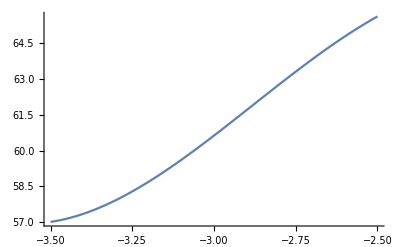

```mathematica
Plot[Abs[f'[x]],{x,-3.5,-2.5}]
```

От геометрично съображение минимумът на абсолютната стойност на първата производна се достига в левия край на интервала, а максимумът - в десния.

```mathematica
M1 = Abs[f'[-2.5]]
```

65.6282

```mathematica
m1 = Abs[f'[-3.5]]
```

57.0132

```mathematica
R = (M1 - m1)/m1
```

0.151105

#### Итериране

```mathematica
M1 = Abs[f'[-2.5]];
m1 = Abs[f'[-3.5]];
R = (M1 - m1)/m1;
f[x_] := -2 x^3 -47Cos[x] - 70
p = -2.5; x0 = -3.5;
epszad = 0.00001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x_n) = ", N[f[x0]]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = -3.5 f(x_n) = 59.7635

n = 1 x_n = -2.51801 f(x_n) = 0.0846361 ε_n = 0.148384

n = 2 x_n = -2.51672 f(x_n) = 0.0000845987 ε_n = 0.000195078

n = 3 x_n = -2.51672 f(x_n) = 8.44756×10^-8 ε_n = 1.94976×10^-7

### 8. Да се провери колко итерации биха били необходими, ако се използва методът на разполовяването в същия интервал [p, q] за същата точност.

```mathematica
Log2[(-2.5 +3.5)/0.00001] - 1
```

15.6096

### 9. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на разполовяването биха били необходими 16 итерации за достигане на исканата точност. А по метода на хордите бяха необходими 3 итерации. Следователно методът на хордите е по-ефективен за избрания интервал [-3.5, -2.5].